```mathematica
SetDirectory[NotebookDirectory[]];
Nc=3.;
mf2[h_,ρ_]:=(h^2 ρ)/2;
pF[μ_,h_,ρ_]:=√(μ^2-mf2[h,ρ]);
gamma[ps_,ρ_,h_,μ_,Mmass_,MZ_]:=(Nc h^2)/(8 π^2)(2 μ pF[μ,h,ρ]+mf2[h,ρ] Log[(μ-pF[μ,h,ρ])/(μ+pF[μ,h,ρ])]+1/2 ps^2((√(ps^2+4 mf2[h,ρ])-2 μ)/ps Log[Abs[(ps+2 pF[μ,h,ρ])/(ps-2pF[μ,h,ρ])]](*-Log[(pF[μ,h,ρ]+μ)^2/mf2[h,ρ]]+(√(ps^2+4 mf2[h,ρ]))/ps Log[(2 mf2[h,ρ]+ps pF[μ,h,ρ]+μ √(ps^2+4 mf2[h,ρ]))/(2 mf2[h,ρ]-ps pF[μ,h,ρ]+μ √(ps^2+4 mf2[h,ρ]))]*)));
gamma2[p0_,ps_,ρ_,ρ0_,h_,μ_,Mmass_,MZ_]:=(*ps^2+(λ300 ρ+ν300)+*)gamma[ps,ρ,h,μ,Mmass,MZ](*+gammavac[ps,ρ,h,Mmass,MZ]-(gammavac[ps,ρ0,h,Mmass,MZ]-gammavacp0[ρ0,h,Mmass,MZ])*);
λ300=75.8;
ν300=-482.^2;
```

```mathematica
CloseKernels[];
LaunchKernels[18];
$KernelCount
```

18

## Finite mu

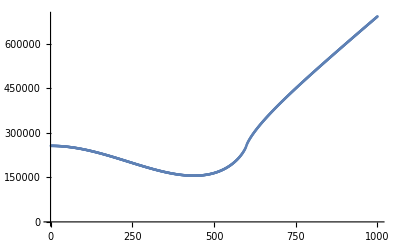

```mathematica
Table[gamma2[0.,N[i],fpi[[10]]^2/2,92.57845450044942^2/2,6.5,mu[[10]],300,300],{i,1,1000,1}];
ListPlot[%]
```

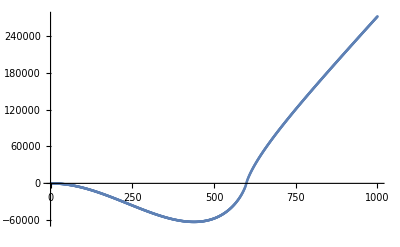

```mathematica
Table[gamma2[0.,N[i],fpi[[10]]^2/2,92.57845450044942^2/2,6.5,mu[[10]],300,300],{i,1,1000,1}];
ListPlot[%]
```

```mathematica
fpi=Flatten[Import["./fpiT1.dat"]];
mu=Table[300+1*i,{i,1,150}];
Length[mu]
```

150

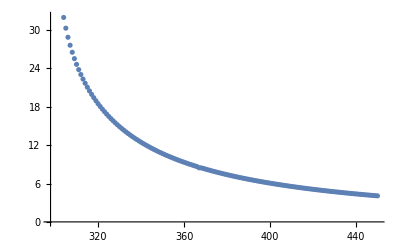

```mathematica
ListPlot[Transpose[{mu,fpi}]]
```

```mathematica
Emu=ParallelTable[Table[gamma2[0.,N[i],fpi[[j]]^2/2,92.57845450044942^2/2,6.5,mu[[j]],300,300]-gamma2[0.,1,fpi[[j]]^2/2,92.57845450044942^2/2,6.5,mu[[j]],300,300],{i,1,1000,5}],{j,2,150,20}];
```

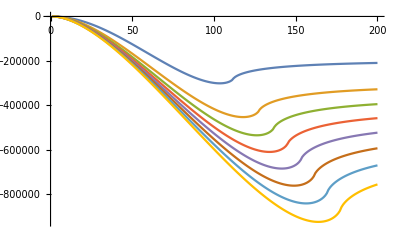

```mathematica
ListLinePlot[Emu]
```

```mathematica
mf=Table[√mf2[6.5,fpi[[i]]^2/2],{i,2,150,20}]
```

{119.633,57.2887,39.1929,29.5469,23.4917,19.3322,16.3039,14.0059}

```mathematica
mu2=Table[mu[[i]],{i,2,150,20}]
```

{302,322,342,362,382,402,422,442}

```mathematica
pfermi=√(mu2^2-mf^2)
```

{277.294,316.863,339.747,360.792,381.277,401.535,421.685,441.778}

```mathematica
ps=Table[i,{i,1,1000,5}]
```

{1,6,11,16,21,26,31,36,41,46,51,56,61,66,71,76,81,86,91,96,101,106,111,116,121,126,131,136,141,146,151,156,161,166,171,176,181,186,191,196,201,206,211,216,221,226,231,236,241,246,251,256,261,266,271,276,281,286,291,296,301,306,311,316,321,326,331,336,341,346,351,356,361,366,371,376,381,386,391,396,401,406,411,416,421,426,431,436,441,446,451,456,461,466,471,476,481,486,491,496,501,506,511,516,521,526,531,536,541,546,551,556,561,566,571,576,581,586,591,596,601,606,611,616,621,626,631,636,641,646,651,656,661,666,671,676,681,686,691,696,701,706,711,716,721,726,731,736,741,746,751,756,761,766,771,776,781,786,791,796,801,806,811,816,821,826,831,836,841,846,851,856,861,866,871,876,881,886,891,896,901,906,911,916,921,926,931,936,941,946,951,956,961,966,971,976,981,986,991,996}

```mathematica
Export["pFT0_mu2.dat",pfermi]
Export["Ethermal.dat",Emu]
Export["ps_thermal.dat",ps]
```

pFT0_mu2.dat

Ethermal.dat

ps_thermal.dat